```mathematica
ClearAll["Global`*"]
```

```mathematica
JB[x_]:=NIntegrate[z^2*Log[1-Exp[-Sqrt[z^2+x]]],{z,0,Infinity}]
(*bosonic field contributions*)
JF[x_]:=NIntegrate[z^2*Log[1+Exp[-Sqrt[z^2+x]]],{z,0,Infinity}]
(*fermionic field contributions*)
(*Cross check*)
fit11=Table[{ϕ,JB[ϕ]},{ϕ,10^(-1),200,.1}];
JBfit11[ϕ_]=Fit[fit11,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit12=Table[{ϕ,JB[ϕ]},{ϕ,10^(-3),10^(-1),10^(-3)}];
JBfit12[ϕ_]=Fit[fit12,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit13=Table[{ϕ,JB[ϕ]},{ϕ,0,10^(-3),10^(-6)}];
JBfit13[ϕ_]=Fit[fit13,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit21=Table[{ϕ,JF[ϕ]},{ϕ,10^(-1),200,.1}];
JFfit21[ϕ_]=Fit[fit21,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit22=Table[{ϕ,JF[ϕ]},{ϕ,10^(-3),10^(-1),10^(-3)}];
JFfit22[ϕ_]=Fit[fit22,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit23=Table[{ϕ,JF[ϕ]},{ϕ,0,10^(-3),10^(-6)}];
JFfit23[ϕ_]=Fit[fit23,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
JBfit[x_/;10^(-1)<x≤200]=JBfit11[x];
JBfit[x_/;10^(-3)<=x≤10^(-1)]=JBfit12[x];
JBfit[x_/;0<=x≤10^(-3)]=JBfit13[x];
JBfit[x_0/;200<x]=0;
JFfit[x_/;10^(-1)<x≤200]=JFfit21[x];
JFfit[x_/;10^(-3)<=x≤10^(-1)]=JFfit22[x];
JFfit[x_/;0<=x≤10^(-3)]=JFfit23[x];
JFfit[x_/;200<x]=0;
```

```mathematica
mH=35;
v0=246;
λ=mH^2/(2 v0^2);
g=0.65;
gY=0.36;
yt=(√2)/246 173;
mW[ϕ_]:=1/4 g^2 ϕ^2;
mZ[ϕ_]:=1/4(g^2+gY^2)ϕ^2;
mt[ϕ_]:=1/2 yt^2 ϕ^2;
V0[ϕ_]:=λ/4 ϕ^4-1/4 mH^2 ϕ^2;
VFT[ϕ_,T_]:=T^4/(2 π^2)(6JBfit[mW[ϕ]/T^2]+3JBfit[mZ[ϕ]/T^2]-12JFfit[mt[ϕ]/T^2]);
B=3/(64 π^2 v0^4)(2 mW[v0]^2+mZ[v0]^2-4 mt[v0]^2);
VCW[ϕ_]:=2B v0^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/v0^2];
Vmytot[ϕ_,T_]:=V0[ϕ]+VFT[ϕ,T];
DD=1/(8 v0^2)(2mW[v0]+mZ[v0]+2mt[v0]);
EE=1/(6π v0^3)(2 mW[v0]^(3/2)+mZ[v0]^(3/2));
EEnoreduc=1/(4π v0^3)(2 mW[v0]^(3/2)+mZ[v0]^(3/2));
T02=1/(4DD)(mH^2-8B v0^2);
T02noCW=1/(4DD)(mH^2);
λT[T_]:=λ-3/(16 π^2 v0^4)(2 mW[v0]^2 Log[mW[v0]/(T^2 ⅇ^3.91)]+mZ[v0]^2 Log[mZ[v0]/(T^2 ⅇ^3.91)]-4 mt[v0]^2 Log[mt[v0]/(T^2 ⅇ^1.14)]);
VhighTDine[ϕ_,T_]:=DD(T^2-T02)ϕ^2-EEnoreduc T ϕ^3+λT[T]/4 ϕ^4;
VfullDine[ϕ_,T_]:=V0[ϕ]+VCW[ϕ]+VFT[ϕ,T]-(V0[10^-5]+VCW[10^-5]+VFT[10^-5,T]);
VhighT[ϕ_,T_]:=DD(T^2-T02noCW)ϕ^2-EE T ϕ^3+λ/4 ϕ^4;
VhighTnoreduc[ϕ_,T_]:=DD(T^2-T02noCW)ϕ^2-EEnoreduc T ϕ^3+λ/4 ϕ^4;
V0bare[λ0_,μ_,ϕ_]:=1/4 λ0 ϕ^4-1/2 μ^2 ϕ^2;
Q=150;
VCWMS[λ0_,μ_,ϕ_]:=1/(64 π^2)(6 mW[ϕ]^2(Log[mW[ϕ]/Q^2]-5/6)+3 mZ[ϕ]^2(Log[mZ[ϕ]/Q^2]-5/6)-12 mt[ϕ]^2(Log[mt[ϕ]/Q^2]-3/2));
V0pre[λ0_,μ_,ϕ_]:=V0bare[λ0,μ,ϕ]+VCWMS[λ0,μ,ϕ];
mass=D[V0pre[λ0,μ,ϕ],{ϕ,2}]/.{ϕ->v0};
derivative=D[V0pre[λ0,μ,ϕ],ϕ]/.{ϕ->v0};
{λMS,μMS}={λ0,μ}/.NSolve[{mass==mH^2,derivative==0},{λ0,μ}][[1]];
V0MS[ϕ_]=V0pre[λMS,μMS,ϕ];
VMS[ϕ_,T_]:=V0MS[ϕ]+VFT[ϕ,T]
```

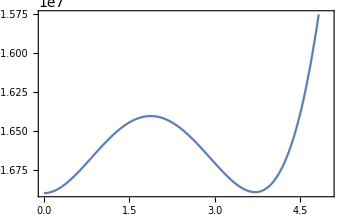

```mathematica
Ttry=53.02;
Plot[Vmytot[x Ttry,Ttry],{x,0,5.0}](*mH=35*)
```

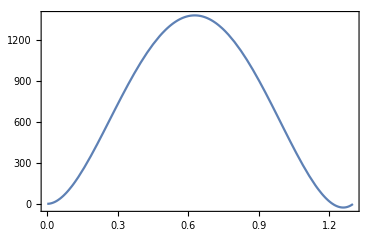

```mathematica
Ttry=43.305;
Plot[VhighT[x Ttry,Ttry],{x,0,1.3}] (*mH=35*)
```

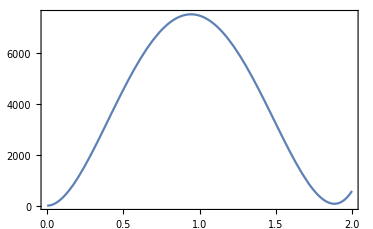

```mathematica
Ttry=43.985;
Plot[VhighTnoreduc[x Ttry,Ttry],{x,0,2.0}] (*mH=35*)
```

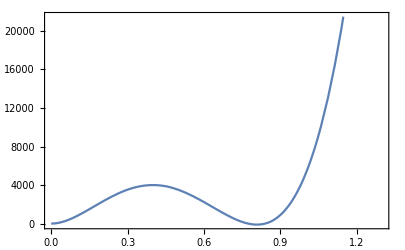

```mathematica
Ttry=71.88;
Plot[{VfullDine[x Ttry,Ttry]},{x,0,1.3}](*mH=20*)
```

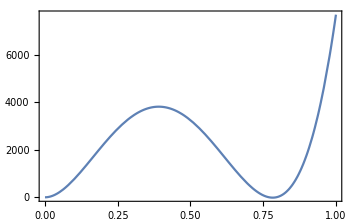

```mathematica
Ttry=71.87;
Plot[VhighTDine[x Ttry, Ttry],{x,0,1.}](*mH=20*)
```

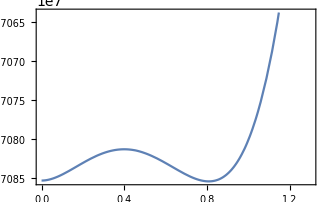

```mathematica
Ttry=71.88;
Plot[VMS[x Ttry,Ttry],{x,0,1.3}](*mH-20*)
```